# Rosenbrock Test Functions

The Rosenbrock function is an analytically simple but computationally tortuous optimization test problem.  It is analytic and has computable derivatives.

```mathematica
Rosen[x_]:= Module[{n=Length[x]},
Sum[(1-x⟦i⟧)^2+100(x⟦i+1⟧-x⟦i⟧^2)^2,{i,1,n-1}]
]
dRosen[x_]:= Module[{n=Length[x],d1},
d1=Join[
Table[-2*(1-x⟦i⟧)-400*x⟦i⟧(x⟦i+1⟧-x⟦i⟧^2),{i,1,n-1}],
{-200*(x[[n-1]]^2-x[[n]])}];
d1⟦2;;-2⟧+=Table[-200*(x[[i-1]]^2-x[[i]]),{i,2,n-1}];
d1
]
ddRosen[x_]:= Module[{n=Length[x],d1},
SparseArray[{
{1,1}->2+800 x[[1]]^2-400 (-x[[1]]^2+x[[2]]),
{n,n}->200, 
Band[{2,2},{n-1,-1}]->Table[202+800 x[[i]]^2-400 (-x[[i]]^2+x[[i+1]]),
{i,2,n-1}],
Band[{2,1}]->-400*x⟦1;;-2⟧,Band[{1,2}]->-400*x⟦1;;-2⟧},
{n,n}]
]
```

It is ALWAYS worth checking derivatives.  You can do things analytically sometimes in Mathematica.

```mathematica
Clear[xx]
n=5;Vars=Array[xx,n];
Simplify[D[Rosen[Vars],{Vars}]-dRosen[Vars]]
MatrixForm[D[Rosen[Vars],{Vars,2}]-ddRosen[Vars]]
```

{0,0,0,0,0}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

You can always check numerically with finite differences.

### Directional 1st derivatives.

If I pick a point and a direction I can approximate the directional derivative by a finite difference and compare it to the analytic formula ∇f.u.

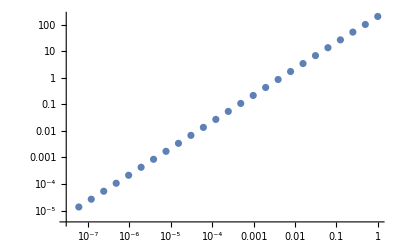

```mathematica
n=5;
{x,u}=RandomReal[{-1,1},{2,n}];
u=Normalize[u];
ListLogLogPlot[
Table[ {ϵ, Abs[(Rosen[x+ϵ u]-Rosen[x])/ϵ-dRosen[x].u]},
{ϵ,2^(-Range[0.0,24])}]
]
```

### Directional 2nd derivatives.

If I pick a point and two directions I can approximate the directional second derivative by a finite difference and compare it to the analytic formula ∇^2 f.u.v=v.∇^2 f.u.

```mathematica
n=5;
{x,u,v}=RandomReal[{-1,1},{2,n}];
{u,v}=Map[Normalize,{u,v}];
ListLogLogPlot[
Table[ {ϵ, Abs[□/□-ddRosen[x].u.v]},
{ϵ,2^(-Range[0.0,24])}]
]
```